## Seebeck

```mathematica
Data=Import["/Users/bobbymckinney/Desktop/seebecktestdata.csv"]
```

{{temperature (C),seebeck_chromel (uV/K)},{50.68,200.497},{80.59,210.695},{110.46,216.83},{140.307,221.},{170.517,219.397},{200.62,216.142},{230.501,212.779},{260.812,209.067},{290.569,202.595},{320.567,191.816},{350.702,177.058},{380.597,161.407},{410.509,143.93},{440.612,125.556},{470.615,106.524},{500.508,89.1044},{470.625,116.761},{440.559,135.591},{410.478,153.195},{380.682,168.784},{350.679,184.104},{320.564,198.873},{290.6,210.964},{260.582,217.615},{230.429,221.073},{200.381,221.684},{170.374,220.949},{140.28,216.211},{110.318,209.502},{80.4006,203.953},{49.8739,198.961}}

```mathematica
Data=Delete[Data,1]
```

{{50.68,200.497},{80.59,210.695},{110.46,216.83},{140.307,221.},{170.517,219.397},{200.62,216.142},{230.501,212.779},{260.812,209.067},{290.569,202.595},{320.567,191.816},{350.702,177.058},{380.597,161.407},{410.509,143.93},{440.612,125.556},{470.615,106.524},{500.508,89.1044},{470.625,116.761},{440.559,135.591},{410.478,153.195},{380.682,168.784},{350.679,184.104},{320.564,198.873},{290.6,210.964},{260.582,217.615},{230.429,221.073},{200.381,221.684},{170.374,220.949},{140.28,216.211},{110.318,209.502},{80.4006,203.953},{49.8739,198.961}}

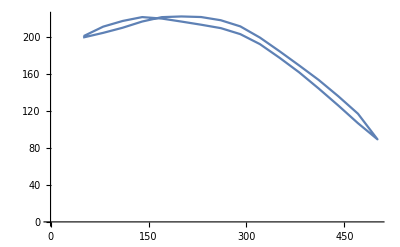

```mathematica
ListPlot[Data,Joined->True]
```

```mathematica
PFit=Fit[Data,{1,x,x^2,x^3},x]
```

176.464+0.507608 x-0.00149715 x^2+2.57013×10^-7 x^3

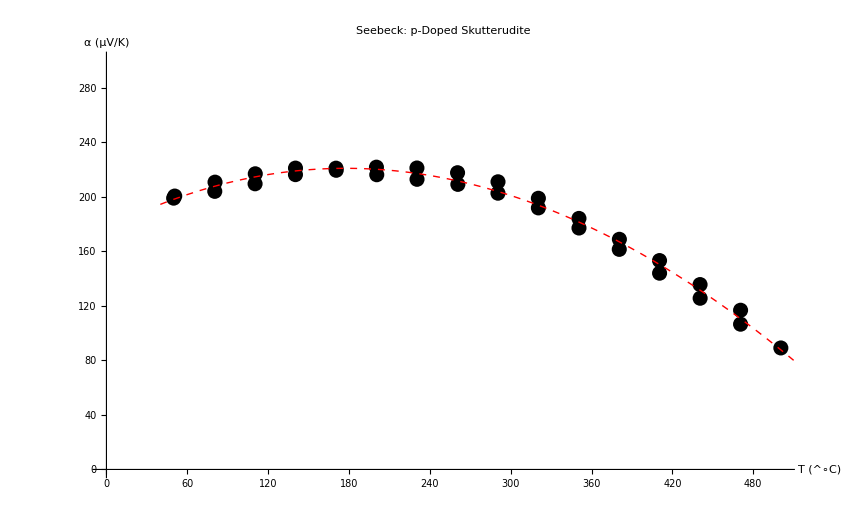

```mathematica
Show[ListPlot[Data,PlotRange->{0,300},PlotStyle->Black,AxesLabel->{"T (^∘C)","α (μV/K)"},PlotLabel->"Seebeck: p-Doped Skutterudite",LabelStyle->{FontFamily->"Arial",27,GrayLevel[0],Bold},Frame->All],Plot[PFit,{x,40,510},PlotStyle->Directive[Red,Thick, Dashed]]]
```

## Voltage

```mathematica
Data=Import["/Users/bobbymckinney/Desktop/voltagetestdata440p64Ch.csv"]
```

{{deltatemp (C),Vchromel (uV)},{-5.3376,-734.102},{-5.3138,-708.119},{-5.3259,-744.031},{-4.6637,-598.753},{-4.1757,-579.606},{-3.8343,-523.061},{-2.9913,-424.605},{-2.9331,-380.351},{-2.6915,-344.5},{-1.7597,-257.471},{-1.3868,-131.57},{-1.2545,-134.803},{-0.849,-115.81},{-0.6424,-50.2581},{0.4226,48.15},{0.5718,114.538},{1.097,187.181},{1.7771,224.88},{1.8871,290.003},{2.2994,327.316},{2.7905,346.374},{2.8829,411.135},{3.8678,515.113},{4.218,586.164},{4.7036,632.187},{5.2405,681.521},{5.4386,730.228},{5.4681,752.083}}

```mathematica
Data=Delete[Data,1]
```

{{-5.3376,-734.102},{-5.3138,-708.119},{-5.3259,-744.031},{-4.6637,-598.753},{-4.1757,-579.606},{-3.8343,-523.061},{-2.9913,-424.605},{-2.9331,-380.351},{-2.6915,-344.5},{-1.7597,-257.471},{-1.3868,-131.57},{-1.2545,-134.803},{-0.849,-115.81},{-0.6424,-50.2581},{0.4226,48.15},{0.5718,114.538},{1.097,187.181},{1.7771,224.88},{1.8871,290.003},{2.2994,327.316},{2.7905,346.374},{2.8829,411.135},{3.8678,515.113},{4.218,586.164},{4.7036,632.187},{5.2405,681.521},{5.4386,730.228},{5.4681,752.083}}

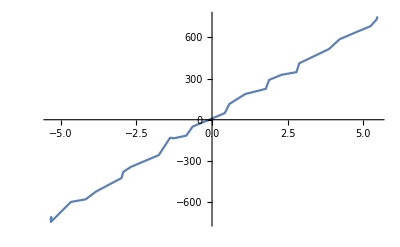

```mathematica
ListPlot[Data,Joined->True]
```

```mathematica
PFit=Fit[Data,{1,x},x]
```

6.66435+135.079 x

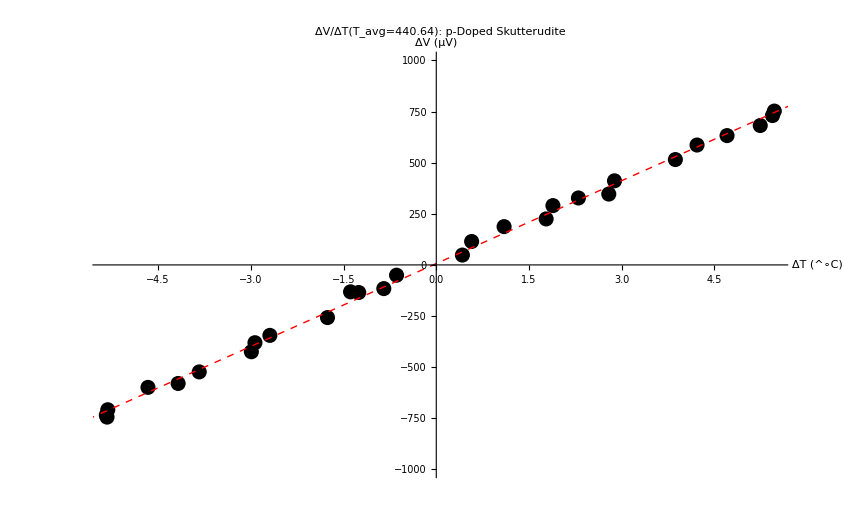

```mathematica
Show[ListPlot[Data,PlotRange->{-1000,1000},PlotStyle->Black,AxesLabel->{"ΔT (^∘C)","ΔV (μV)"},PlotLabel->"ΔV/ΔT(T_avg=440.64): p-Doped Skutterudite",LabelStyle->{FontFamily->"Arial",27,GrayLevel[0],Bold},Frame->All],Plot[PFit,{x,-8,8},PlotStyle->Directive[Red,Thick, Dashed]]]
```

## Resistivity

```mathematica
Data=Import["/Users/bobbymckinney/Desktop/resistivitytestdata.csv"]
```

{{sample temp (C),resistivity (mOhm*cm)},{27.45,2.07385},{31.2,2.07951},{35.65,2.08844},{39.2,2.09828},{42.45,2.10829},{46.8,2.11961},{52.05,2.13315},{57.85,2.14871},{64.25,2.16592},{70.9,2.18493},{77.8,2.20489},{84.85,2.22563},{92.1,2.24692},{99.45,2.26958},{106.8,2.29201},{114,2.31497},{121.4,2.33826},{128.8,2.36169},{136.2,2.38484},{143.5,2.40906},{150.7,2.43297},{157.85,2.45718},{164.9,2.481},{172.05,2.50498},{178.95,2.52855},{185.8,2.55252},{192.6,2.57614},{199.4,2.59971},{206.05,2.62384},{212.8,2.64746},{219.4,2.67144},{226,2.69467},{232.55,2.71846},{238.85,2.74181},{245.2,2.76524},{251.55,2.78866},{257.85,2.81218},{264.05,2.8362},{270.35,2.85932},{276.65,2.8825},{282.85,2.90621},{288.8,2.92974},{294.8,2.95305},{300.75,2.9751},{306.65,2.99887},{312.6,3.02233},{318.4,3.04449},{324.25,3.06769},{329.85,3.09172},{335.5,3.11385},{341.2,3.13672},{346.65,3.159},{352.05,3.18158},{357.25,3.20179},{362.5,3.22346},{367.7,3.24544},{372.9,3.26844},{378.05,3.28749},{382.95,3.30682},{387.75,3.32647},{392.45,3.34568},{396.9,3.36637},{401.35,3.38382},{405.75,3.40358},{410.15,3.42193},{414.7,3.43968},{419.15,3.46012},{423.55,3.47758},{427.85,3.49632},{433.25,3.52085},{441.3,3.55402},{449.3,3.58777},{456.2,3.61715},{461.95,3.64233},{466.85,3.66472},{471.2,3.68459},{475.2,3.70305},{479,3.7207},{482.6,3.73419},{486.15,3.75134},{490.2,3.77467},{494.15,3.78952},{497.15,3.80208},{499.25,3.81109},{500.5,3.81559},{500.85,3.81912},{501.4,3.82292},{502.15,3.82565},{502.45,3.82658},{502.65,3.82651},{502.9,3.82821},{502.55,3.82631},{501.25,3.81826},{499.3,3.80913},{496.7,3.79991},{493.7,3.78562},{490.45,3.77315},{487,3.75611},{483.35,3.74001},{479.6,3.72582},{475.65,3.70668},{471.95,3.6926},{468.2,3.67304},{464.1,3.65691},{459.75,3.638},{455.45,3.61834},{451.1,3.59362},{446.65,3.5838},{442.05,3.56308},{437.3,3.54074},{432.55,3.52414},{427.85,3.50296},{423.25,3.48272},{418.5,3.46262},{413.65,3.44374},{408.65,3.41881},{403.4,3.40266},{398.25,3.37974},{393.05,3.35883},{387.75,3.33731},{382.15,3.31528},{375.75,3.29244},{369.95,3.26577},{364.55,3.24686},{358.85,3.22357},{353.35,3.20291},{347.7,3.18129},{341.95,3.15793},{336.2,3.13712},{330.3,3.11493},{324.1,3.09015},{317.65,3.06798},{311.35,3.04366},{305,3.01997},{298.75,2.99641},{292.35,2.97264},{285.95,2.94971},{279.15,2.9263},{270.75,2.90249},{262.15,2.877},{255.15,2.85308},{248.75,2.83302},{242.55,2.80763},{236.35,2.78429},{229.95,2.76066},{223.45,2.73717},{216.8,2.7145},{210.05,2.69116},{203.35,2.66783},{196.55,2.64462},{189.65,2.62089},{182.65,2.59784},{175.7,2.57407},{168.7,2.55006},{161.6,2.52693},{154.45,2.50308},{147.1,2.48},{139.75,2.45707},{132.35,2.43143},{124.75,2.40501},{117.25,2.38175},{109.75,2.36249},{102.2,2.33708},{94.8,2.31477},{87.75,2.29278},{81.35,2.27217},{75.55,2.25317},{70.3,2.23584},{65.6,2.2198},{61.5,2.20567},{57.85,2.19344},{54.6,2.18253},{51.7,2.17229},{49.2,2.1625},{46.9,2.15435},{44.9,2.14628},{43.05,2.14012},{41.5,2.13431},{40.15,2.12869},{38.8,2.12387},{37.6,2.11948},{36.55,2.11546},{35.6,2.11216},{34.7,2.10908},{34,2.10653}}

```mathematica
Data=Delete[Data,1]
```

{{27.45,2.07385},{31.2,2.07951},{35.65,2.08844},{39.2,2.09828},{42.45,2.10829},{46.8,2.11961},{52.05,2.13315},{57.85,2.14871},{64.25,2.16592},{70.9,2.18493},{77.8,2.20489},{84.85,2.22563},{92.1,2.24692},{99.45,2.26958},{106.8,2.29201},{114,2.31497},{121.4,2.33826},{128.8,2.36169},{136.2,2.38484},{143.5,2.40906},{150.7,2.43297},{157.85,2.45718},{164.9,2.481},{172.05,2.50498},{178.95,2.52855},{185.8,2.55252},{192.6,2.57614},{199.4,2.59971},{206.05,2.62384},{212.8,2.64746},{219.4,2.67144},{226,2.69467},{232.55,2.71846},{238.85,2.74181},{245.2,2.76524},{251.55,2.78866},{257.85,2.81218},{264.05,2.8362},{270.35,2.85932},{276.65,2.8825},{282.85,2.90621},{288.8,2.92974},{294.8,2.95305},{300.75,2.9751},{306.65,2.99887},{312.6,3.02233},{318.4,3.04449},{324.25,3.06769},{329.85,3.09172},{335.5,3.11385},{341.2,3.13672},{346.65,3.159},{352.05,3.18158},{357.25,3.20179},{362.5,3.22346},{367.7,3.24544},{372.9,3.26844},{378.05,3.28749},{382.95,3.30682},{387.75,3.32647},{392.45,3.34568},{396.9,3.36637},{401.35,3.38382},{405.75,3.40358},{410.15,3.42193},{414.7,3.43968},{419.15,3.46012},{423.55,3.47758},{427.85,3.49632},{433.25,3.52085},{441.3,3.55402},{449.3,3.58777},{456.2,3.61715},{461.95,3.64233},{466.85,3.66472},{471.2,3.68459},{475.2,3.70305},{479,3.7207},{482.6,3.73419},{486.15,3.75134},{490.2,3.77467},{494.15,3.78952},{497.15,3.80208},{499.25,3.81109},{500.5,3.81559},{500.85,3.81912},{501.4,3.82292},{502.15,3.82565},{502.45,3.82658},{502.65,3.82651},{502.9,3.82821},{502.55,3.82631},{501.25,3.81826},{499.3,3.80913},{496.7,3.79991},{493.7,3.78562},{490.45,3.77315},{487,3.75611},{483.35,3.74001},{479.6,3.72582},{475.65,3.70668},{471.95,3.6926},{468.2,3.67304},{464.1,3.65691},{459.75,3.638},{455.45,3.61834},{451.1,3.59362},{446.65,3.5838},{442.05,3.56308},{437.3,3.54074},{432.55,3.52414},{427.85,3.50296},{423.25,3.48272},{418.5,3.46262},{413.65,3.44374},{408.65,3.41881},{403.4,3.40266},{398.25,3.37974},{393.05,3.35883},{387.75,3.33731},{382.15,3.31528},{375.75,3.29244},{369.95,3.26577},{364.55,3.24686},{358.85,3.22357},{353.35,3.20291},{347.7,3.18129},{341.95,3.15793},{336.2,3.13712},{330.3,3.11493},{324.1,3.09015},{317.65,3.06798},{311.35,3.04366},{305,3.01997},{298.75,2.99641},{292.35,2.97264},{285.95,2.94971},{279.15,2.9263},{270.75,2.90249},{262.15,2.877},{255.15,2.85308},{248.75,2.83302},{242.55,2.80763},{236.35,2.78429},{229.95,2.76066},{223.45,2.73717},{216.8,2.7145},{210.05,2.69116},{203.35,2.66783},{196.55,2.64462},{189.65,2.62089},{182.65,2.59784},{175.7,2.57407},{168.7,2.55006},{161.6,2.52693},{154.45,2.50308},{147.1,2.48},{139.75,2.45707},{132.35,2.43143},{124.75,2.40501},{117.25,2.38175},{109.75,2.36249},{102.2,2.33708},{94.8,2.31477},{87.75,2.29278},{81.35,2.27217},{75.55,2.25317},{70.3,2.23584},{65.6,2.2198},{61.5,2.20567},{57.85,2.19344},{54.6,2.18253},{51.7,2.17229},{49.2,2.1625},{46.9,2.15435},{44.9,2.14628},{43.05,2.14012},{41.5,2.13431},{40.15,2.12869},{38.8,2.12387},{37.6,2.11948},{36.55,2.11546},{35.6,2.11216},{34.7,2.10908},{34,2.10653}}

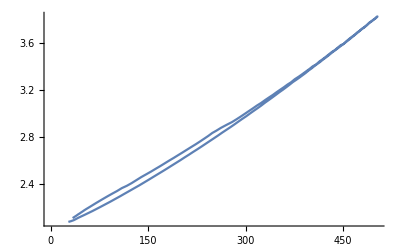

```mathematica
ListPlot[Data,Joined->True]
```

```mathematica
PFit=Fit[Data,{1,x,x^2,x^3},x]
```

2.00525+0.00282868 x+1.35933×10^-6 x^2+4.42835×10^-10 x^3

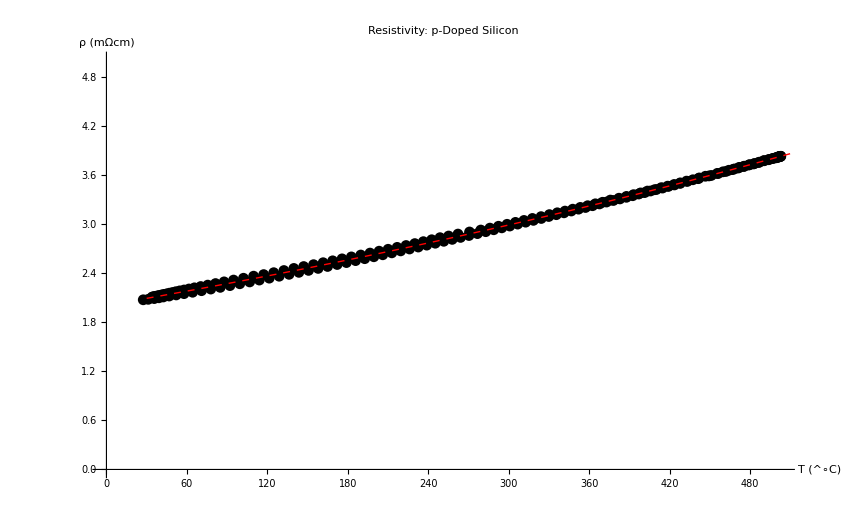

```mathematica
Show[ListPlot[Data,PlotRange->{0,5},PlotStyle->Black,AxesLabel->{"T (^∘C)","ρ (mΩcm)"},PlotLabel->"Resistivity: p-Doped Silicon",LabelStyle->{FontFamily->"Arial",27,GrayLevel[0],Bold},Frame->All],Plot[PFit,{x,30,510},PlotStyle->Directive[Red,Thick, Dashed]]]
```

## Carrier

```mathematica
Data=Import["/Users/bobbymckinney/Desktop/carriertestdata.csv"]
```

{{sample temp (C),Carrier Concentration (cm^-3)},{27.45,6.82498×10^19},{31.2,6.84697×10^19},{35.65,6.80529×10^19},{39.2,6.81534×10^19},{42.45,6.87095×10^19},{46.8,6.81819×10^19},{52.05,6.79821×10^19},{57.85,6.80318×10^19},{64.25,6.82761×10^19},{70.9,6.80109×10^19},{77.8,6.90541×10^19},{84.85,6.91577×10^19},{92.1,6.84442×10^19},{99.45,6.88495×10^19},{106.8,6.84373×10^19},{114,6.94564×10^19},{121.4,6.84452×10^19},{128.8,6.8872×10^19},{136.2,6.8777×10^19},{143.5,6.93066×10^19},{150.7,6.89546×10^19},{157.85,6.89146×10^19},{164.9,6.90366×10^19},{172.05,6.89716×10^19},{178.95,6.98539×10^19},{185.8,6.96288×10^19},{192.6,6.97496×10^19},{199.4,6.96422×10^19},{206.05,6.9561×10^19},{212.8,7.03408×10^19},{219.4,7.25856×10^19},{226,7.05865×10^19},{232.55,6.94962×10^19},{238.85,6.9343×10^19},{245.2,7.0357×10^19},{251.55,7.02694×10^19},{257.85,7.07473×10^19},{264.05,7.3878×10^19},{270.35,7.12278×10^19},{276.65,7.21237×10^19},{282.85,7.15059×10^19},{288.8,7.45125×10^19},{294.8,7.48253×10^19},{300.75,6.7233×10^19},{306.65,6.88354×10^19},{312.6,7.07619×10^19},{318.4,7.13649×10^19},{324.25,7.23902×10^19},{329.85,7.65212×10^19},{335.5,7.20503×10^19},{341.2,7.11202×10^19},{346.65,7.17613×10^19},{352.05,7.27885×10^19},{357.25,7.24551×10^19},{362.5,7.13214×10^19},{367.7,7.66441×10^19},{372.9,7.34109×10^19},{378.05,7.31063×10^19},{382.95,7.23439×10^19},{387.75,7.2255×10^19},{392.45,7.41725×10^19},{396.9,7.2766×10^19},{401.35,7.24047×10^19},{405.75,7.68597×10^19},{410.15,7.28036×10^19},{414.7,7.33157×10^19},{419.15,7.37269×10^19},{423.55,7.36951×10^19},{427.85,7.37497×10^19},{433.25,7.37125×10^19},{441.3,7.27742×10^19},{449.3,7.44204×10^19},{456.2,7.50099×10^19},{461.95,8.1869×10^19},{466.85,7.63305×10^19},{471.2,8.00511×10^19},{475.2,7.95635×10^19},{479,7.5061×10^19},{482.6,8.2844×10^19},{486.15,7.73668×10^19},{490.2,7.4785×10^19},{494.15,7.42561×10^19},{497.15,7.53998×10^19},{499.25,8.19277×10^19},{500.5,8.06968×10^19},{500.85,8.21694×10^19},{501.4,7.11304×10^19},{502.15,8.14828×10^19},{502.45,7.57129×10^19},{502.65,7.5458×10^19},{502.9,7.35488×10^19},{502.55,8.19158×10^19},{501.25,8.36832×10^19},{499.3,7.18078×10^19},{496.7,7.68693×10^19},{493.7,8.20484×10^19},{490.45,8.15512×10^19},{487,8.11466×10^19},{483.35,8.15597×10^19},{479.6,7.43818×10^19},{475.65,7.5574×10^19},{471.95,8.06765×10^19},{468.2,7.55373×10^19},{464.1,7.55856×10^19},{459.75,7.95718×10^19},{455.45,8.04236×10^19},{451.1,8.28115×10^19},{446.65,7.24359×10^19},{442.05,7.31997×10^19},{437.3,7.6209×10^19},{432.55,7.61207×10^19},{427.85,8.03853×10^19},{423.25,7.68315×10^19},{418.5,8.01379×10^19},{413.65,8.09465×10^19},{408.65,7.38659×10^19},{403.4,7.30122×10^19},{398.25,7.82927×10^19},{393.05,7.95775×10^19},{387.75,7.5913×10^19},{382.15,7.34173×10^19},{375.75,7.41008×10^19},{369.95,7.48304×10^19},{364.55,7.24141×10^19},{358.85,7.33557×10^19},{353.35,7.26358×10^19},{347.7,7.54567×10^19},{341.95,7.27047×10^19},{336.2,7.30699×10^19},{330.3,7.20191×10^19},{324.1,7.48008×10^19},{317.65,7.58453×10^19},{311.35,7.58864×10^19},{305,7.74766×10^19},{298.75,7.74585×10^19},{292.35,7.76979×10^19},{285.95,7.14191×10^19},{279.15,7.13255×10^19},{270.75,7.60504×10^19},{262.15,7.62052×10^19},{255.15,7.40537×10^19},{248.75,7.49951×10^19},{242.55,7.49046×10^19},{236.35,7.42902×10^19},{229.95,7.45609×10^19},{223.45,7.37393×10^19},{216.8,6.92189×10^19},{210.05,7.08319×10^19},{203.35,7.17599×10^19},{196.55,6.99007×10^19},{189.65,7.28951×10^19},{182.65,7.22356×10^19},{175.7,7.18728×10^19},{168.7,7.15873×10^19},{161.6,7.1543×10^19},{154.45,7.25442×10^19},{147.1,7.16826×10^19},{139.75,7.11418×10^19},{132.35,6.85932×10^19},{124.75,7.1041×10^19},{117.25,7.01847×10^19},{109.75,6.89191×10^19},{102.2,6.89581×10^19},{94.8,6.82301×10^19},{87.75,7.20395×10^19},{81.35,6.81177×10^19},{75.55,6.98929×10^19},{70.3,7.05718×10^19},{65.6,6.87074×10^19},{61.5,6.90837×10^19},{57.85,6.9511×10^19},{54.6,6.88497×10^19},{51.7,6.80406×10^19},{49.2,6.86187×10^19},{46.9,6.93202×10^19},{44.9,6.85085×10^19},{43.05,6.90811×10^19},{41.5,6.87952×10^19},{40.15,6.87873×10^19},{38.8,6.91726×10^19},{37.6,6.87398×10^19},{36.55,6.78719×10^19},{35.6,6.9353×10^19},{34.7,6.94393×10^19},{34,6.93963×10^19}}

```mathematica
Data=Delete[Data,1]
```

{{27.45,6.82498×10^19},{31.2,6.84697×10^19},{35.65,6.80529×10^19},{39.2,6.81534×10^19},{42.45,6.87095×10^19},{46.8,6.81819×10^19},{52.05,6.79821×10^19},{57.85,6.80318×10^19},{64.25,6.82761×10^19},{70.9,6.80109×10^19},{77.8,6.90541×10^19},{84.85,6.91577×10^19},{92.1,6.84442×10^19},{99.45,6.88495×10^19},{106.8,6.84373×10^19},{114,6.94564×10^19},{121.4,6.84452×10^19},{128.8,6.8872×10^19},{136.2,6.8777×10^19},{143.5,6.93066×10^19},{150.7,6.89546×10^19},{157.85,6.89146×10^19},{164.9,6.90366×10^19},{172.05,6.89716×10^19},{178.95,6.98539×10^19},{185.8,6.96288×10^19},{192.6,6.97496×10^19},{199.4,6.96422×10^19},{206.05,6.9561×10^19},{212.8,7.03408×10^19},{219.4,7.25856×10^19},{226,7.05865×10^19},{232.55,6.94962×10^19},{238.85,6.9343×10^19},{245.2,7.0357×10^19},{251.55,7.02694×10^19},{257.85,7.07473×10^19},{264.05,7.3878×10^19},{270.35,7.12278×10^19},{276.65,7.21237×10^19},{282.85,7.15059×10^19},{288.8,7.45125×10^19},{294.8,7.48253×10^19},{300.75,6.7233×10^19},{306.65,6.88354×10^19},{312.6,7.07619×10^19},{318.4,7.13649×10^19},{324.25,7.23902×10^19},{329.85,7.65212×10^19},{335.5,7.20503×10^19},{341.2,7.11202×10^19},{346.65,7.17613×10^19},{352.05,7.27885×10^19},{357.25,7.24551×10^19},{362.5,7.13214×10^19},{367.7,7.66441×10^19},{372.9,7.34109×10^19},{378.05,7.31063×10^19},{382.95,7.23439×10^19},{387.75,7.2255×10^19},{392.45,7.41725×10^19},{396.9,7.2766×10^19},{401.35,7.24047×10^19},{405.75,7.68597×10^19},{410.15,7.28036×10^19},{414.7,7.33157×10^19},{419.15,7.37269×10^19},{423.55,7.36951×10^19},{427.85,7.37497×10^19},{433.25,7.37125×10^19},{441.3,7.27742×10^19},{449.3,7.44204×10^19},{456.2,7.50099×10^19},{461.95,8.1869×10^19},{466.85,7.63305×10^19},{471.2,8.00511×10^19},{475.2,7.95635×10^19},{479,7.5061×10^19},{482.6,8.2844×10^19},{486.15,7.73668×10^19},{490.2,7.4785×10^19},{494.15,7.42561×10^19},{497.15,7.53998×10^19},{499.25,8.19277×10^19},{500.5,8.06968×10^19},{500.85,8.21694×10^19},{501.4,7.11304×10^19},{502.15,8.14828×10^19},{502.45,7.57129×10^19},{502.65,7.5458×10^19},{502.9,7.35488×10^19},{502.55,8.19158×10^19},{501.25,8.36832×10^19},{499.3,7.18078×10^19},{496.7,7.68693×10^19},{493.7,8.20484×10^19},{490.45,8.15512×10^19},{487,8.11466×10^19},{483.35,8.15597×10^19},{479.6,7.43818×10^19},{475.65,7.5574×10^19},{471.95,8.06765×10^19},{468.2,7.55373×10^19},{464.1,7.55856×10^19},{459.75,7.95718×10^19},{455.45,8.04236×10^19},{451.1,8.28115×10^19},{446.65,7.24359×10^19},{442.05,7.31997×10^19},{437.3,7.6209×10^19},{432.55,7.61207×10^19},{427.85,8.03853×10^19},{423.25,7.68315×10^19},{418.5,8.01379×10^19},{413.65,8.09465×10^19},{408.65,7.38659×10^19},{403.4,7.30122×10^19},{398.25,7.82927×10^19},{393.05,7.95775×10^19},{387.75,7.5913×10^19},{382.15,7.34173×10^19},{375.75,7.41008×10^19},{369.95,7.48304×10^19},{364.55,7.24141×10^19},{358.85,7.33557×10^19},{353.35,7.26358×10^19},{347.7,7.54567×10^19},{341.95,7.27047×10^19},{336.2,7.30699×10^19},{330.3,7.20191×10^19},{324.1,7.48008×10^19},{317.65,7.58453×10^19},{311.35,7.58864×10^19},{305,7.74766×10^19},{298.75,7.74585×10^19},{292.35,7.76979×10^19},{285.95,7.14191×10^19},{279.15,7.13255×10^19},{270.75,7.60504×10^19},{262.15,7.62052×10^19},{255.15,7.40537×10^19},{248.75,7.49951×10^19},{242.55,7.49046×10^19},{236.35,7.42902×10^19},{229.95,7.45609×10^19},{223.45,7.37393×10^19},{216.8,6.92189×10^19},{210.05,7.08319×10^19},{203.35,7.17599×10^19},{196.55,6.99007×10^19},{189.65,7.28951×10^19},{182.65,7.22356×10^19},{175.7,7.18728×10^19},{168.7,7.15873×10^19},{161.6,7.1543×10^19},{154.45,7.25442×10^19},{147.1,7.16826×10^19},{139.75,7.11418×10^19},{132.35,6.85932×10^19},{124.75,7.1041×10^19},{117.25,7.01847×10^19},{109.75,6.89191×10^19},{102.2,6.89581×10^19},{94.8,6.82301×10^19},{87.75,7.20395×10^19},{81.35,6.81177×10^19},{75.55,6.98929×10^19},{70.3,7.05718×10^19},{65.6,6.87074×10^19},{61.5,6.90837×10^19},{57.85,6.9511×10^19},{54.6,6.88497×10^19},{51.7,6.80406×10^19},{49.2,6.86187×10^19},{46.9,6.93202×10^19},{44.9,6.85085×10^19},{43.05,6.90811×10^19},{41.5,6.87952×10^19},{40.15,6.87873×10^19},{38.8,6.91726×10^19},{37.6,6.87398×10^19},{36.55,6.78719×10^19},{35.6,6.9353×10^19},{34.7,6.94393×10^19},{34,6.93963×10^19}}

```mathematica
ListPlot[Data,Joined->True]
```

-Graphics-

```mathematica
PFit=Fit[Data,{1,x,x^2,x^3},x]
```

6.77185×10^19+2.07408×10^16 x-3.33737×10^13 x^2+6.9199×10^10 x^3

```mathematica
Show[ListPlot[Data,PlotRange->{0,10^20},PlotStyle->Black,AxesLabel->{"T (^∘C)","𝓃_H (cm^-3)"},PlotLabel->"Hall Concentration: p-Doped Silicon",LabelStyle->{FontFamily->"Arial",27,GrayLevel[0],Bold},Frame->All],Plot[PFit,{x,30,510},PlotStyle->Directive[Red,Thick, Dashed]]]
```

-Graphics-

## Mobility

```mathematica
Data=Import["/Users/bobbymckinney/Desktop/mobilitytestdata.csv"]
```

{{sample temp (C),Mobility (cm^2/Vs)},{27.45,44.1838},{31.2,43.9554},{35.65,44.0698},{39.2,43.8075},{42.45,43.2479},{46.8,43.3627},{52.05,43.2359},{57.85,42.9107},{64.25,42.4325},{70.9,42.2433},{77.8,41.2358},{84.85,40.7957},{92.1,40.8336},{99.45,40.1983},{106.8,40.0406},{114,39.0644},{121.4,39.2475},{128.8,38.6166},{136.2,38.2904},{143.5,37.6224},{150.7,37.4386},{157.85,37.0917},{164.9,36.666},{172.05,36.3488},{178.95,35.5506},{185.8,35.3318},{192.6,34.9433},{199.4,34.6782},{206.05,34.4016},{212.8,33.712},{219.4,32.377},{226,33.0011},{232.55,33.2277},{238.85,33.0136},{245.2,32.2614},{251.55,32.0292},{257.85,31.5462},{264.05,29.9551},{270.35,30.8125},{276.65,30.1844},{282.85,30.1986},{288.8,28.7455},{294.8,28.3973},{300.75,31.3623},{306.65,30.3973},{312.6,29.3378},{318.4,28.8711},{324.25,28.251},{329.85,26.521},{335.5,27.9572},{341.2,28.1189},{346.65,27.6678},{352.05,27.0843},{357.25,27.0266},{362.5,27.2772},{367.7,25.2116},{372.9,26.1402},{378.05,26.0808},{382.95,26.2023},{387.75,26.0803},{392.45,25.2582},{396.9,25.5933},{401.35,25.5757},{405.75,23.9612},{410.15,25.1549},{414.7,24.8478},{419.15,24.5724},{423.55,24.4487},{427.85,24.3038},{433.25,24.1661},{441.3,24.278},{449.3,23.5186},{456.2,23.1293},{461.95,21.0322},{466.85,22.4115},{471.2,21.2469},{475.2,21.2663},{479,22.4322},{482.6,20.2399},{486.15,21.5841},{490.2,22.2091},{494.15,22.2544},{497.15,21.8377},{499.25,20.0407},{500.5,20.3104},{500.85,19.9254},{501.4,22.9956},{502.15,20.0569},{502.45,21.5751},{502.65,21.6455},{502.9,22.2027},{502.55,19.9354},{501.25,19.5397},{499.3,22.8225},{496.7,21.3712},{493.7,20.0842},{490.45,20.2781},{487,20.4591},{483.35,20.4455},{479.6,22.5095},{475.65,22.2537},{471.95,20.9398},{468.2,22.4666},{464.1,22.5616},{459.75,21.5343},{455.45,21.4195},{451.1,20.9299},{446.65,24.0429},{442.05,23.8938},{437.3,23.0894},{432.55,23.2435},{427.85,22.1288},{423.25,23.2896},{418.5,22.4584},{413.65,22.3595},{408.65,24.6593},{403.4,25.0978},{398.25,23.54},{393.05,23.3105},{387.75,24.5906},{382.15,25.593},{375.75,25.5291},{369.95,25.4711},{364.55,26.5052},{358.85,26.3356},{353.35,26.7785},{347.7,25.9481},{341.95,27.1214},{336.2,27.1752},{330.3,27.7613},{324.1,26.9312},{317.65,26.7629},{311.35,26.9518},{305,26.6077},{298.75,26.8229},{292.35,26.9523},{285.95,29.553},{279.15,29.8252},{270.75,28.1988},{262.15,28.3815},{255.15,29.458},{248.75,29.3132},{242.55,29.585},{236.35,30.0897},{229.95,30.2344},{223.45,30.8333},{216.8,33.125},{210.05,32.6462},{203.35,32.5046},{196.55,33.6615},{189.65,32.5665},{182.65,33.1584},{175.7,33.6275},{168.7,34.0764},{161.6,34.4142},{154.45,34.2562},{147.1,34.9944},{139.75,35.5889},{132.35,37.2781},{124.75,36.381},{117.25,37.2071},{109.75,38.2299},{102.2,38.5715},{94.8,39.383},{87.75,37.6591},{81.35,40.1989},{75.55,39.5207},{70.3,39.4574},{65.6,40.8317},{61.5,40.8861},{57.85,40.8782},{54.6,41.4891},{51.7,42.1863},{49.2,42.0242},{46.9,41.7719},{44.9,42.4261},{43.05,42.2142},{41.5,42.5083},{40.15,42.6272},{38.8,42.4939},{37.6,42.8542},{36.55,43.4883},{35.6,42.6333},{34.7,42.6446},{34,42.7281}}

```mathematica
Data=Delete[Data,1]
```

{{27.45,44.1838},{31.2,43.9554},{35.65,44.0698},{39.2,43.8075},{42.45,43.2479},{46.8,43.3627},{52.05,43.2359},{57.85,42.9107},{64.25,42.4325},{70.9,42.2433},{77.8,41.2358},{84.85,40.7957},{92.1,40.8336},{99.45,40.1983},{106.8,40.0406},{114,39.0644},{121.4,39.2475},{128.8,38.6166},{136.2,38.2904},{143.5,37.6224},{150.7,37.4386},{157.85,37.0917},{164.9,36.666},{172.05,36.3488},{178.95,35.5506},{185.8,35.3318},{192.6,34.9433},{199.4,34.6782},{206.05,34.4016},{212.8,33.712},{219.4,32.377},{226,33.0011},{232.55,33.2277},{238.85,33.0136},{245.2,32.2614},{251.55,32.0292},{257.85,31.5462},{264.05,29.9551},{270.35,30.8125},{276.65,30.1844},{282.85,30.1986},{288.8,28.7455},{294.8,28.3973},{300.75,31.3623},{306.65,30.3973},{312.6,29.3378},{318.4,28.8711},{324.25,28.251},{329.85,26.521},{335.5,27.9572},{341.2,28.1189},{346.65,27.6678},{352.05,27.0843},{357.25,27.0266},{362.5,27.2772},{367.7,25.2116},{372.9,26.1402},{378.05,26.0808},{382.95,26.2023},{387.75,26.0803},{392.45,25.2582},{396.9,25.5933},{401.35,25.5757},{405.75,23.9612},{410.15,25.1549},{414.7,24.8478},{419.15,24.5724},{423.55,24.4487},{427.85,24.3038},{433.25,24.1661},{441.3,24.278},{449.3,23.5186},{456.2,23.1293},{461.95,21.0322},{466.85,22.4115},{471.2,21.2469},{475.2,21.2663},{479,22.4322},{482.6,20.2399},{486.15,21.5841},{490.2,22.2091},{494.15,22.2544},{497.15,21.8377},{499.25,20.0407},{500.5,20.3104},{500.85,19.9254},{501.4,22.9956},{502.15,20.0569},{502.45,21.5751},{502.65,21.6455},{502.9,22.2027},{502.55,19.9354},{501.25,19.5397},{499.3,22.8225},{496.7,21.3712},{493.7,20.0842},{490.45,20.2781},{487,20.4591},{483.35,20.4455},{479.6,22.5095},{475.65,22.2537},{471.95,20.9398},{468.2,22.4666},{464.1,22.5616},{459.75,21.5343},{455.45,21.4195},{451.1,20.9299},{446.65,24.0429},{442.05,23.8938},{437.3,23.0894},{432.55,23.2435},{427.85,22.1288},{423.25,23.2896},{418.5,22.4584},{413.65,22.3595},{408.65,24.6593},{403.4,25.0978},{398.25,23.54},{393.05,23.3105},{387.75,24.5906},{382.15,25.593},{375.75,25.5291},{369.95,25.4711},{364.55,26.5052},{358.85,26.3356},{353.35,26.7785},{347.7,25.9481},{341.95,27.1214},{336.2,27.1752},{330.3,27.7613},{324.1,26.9312},{317.65,26.7629},{311.35,26.9518},{305,26.6077},{298.75,26.8229},{292.35,26.9523},{285.95,29.553},{279.15,29.8252},{270.75,28.1988},{262.15,28.3815},{255.15,29.458},{248.75,29.3132},{242.55,29.585},{236.35,30.0897},{229.95,30.2344},{223.45,30.8333},{216.8,33.125},{210.05,32.6462},{203.35,32.5046},{196.55,33.6615},{189.65,32.5665},{182.65,33.1584},{175.7,33.6275},{168.7,34.0764},{161.6,34.4142},{154.45,34.2562},{147.1,34.9944},{139.75,35.5889},{132.35,37.2781},{124.75,36.381},{117.25,37.2071},{109.75,38.2299},{102.2,38.5715},{94.8,39.383},{87.75,37.6591},{81.35,40.1989},{75.55,39.5207},{70.3,39.4574},{65.6,40.8317},{61.5,40.8861},{57.85,40.8782},{54.6,41.4891},{51.7,42.1863},{49.2,42.0242},{46.9,41.7719},{44.9,42.4261},{43.05,42.2142},{41.5,42.5083},{40.15,42.6272},{38.8,42.4939},{37.6,42.8542},{36.55,43.4883},{35.6,42.6333},{34.7,42.6446},{34,42.7281}}

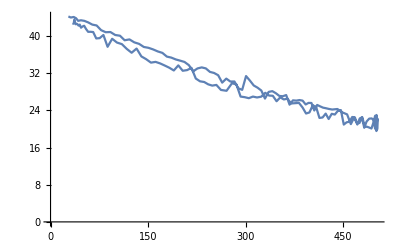

```mathematica
ListPlot[Data,Joined->True]
```

```mathematica
PFit=Fit[Data,{1,x,x^2,x^3},x]
```

45.8014-0.0730203 x+0.0000647857 x^2-3.62884×10^-8 x^3

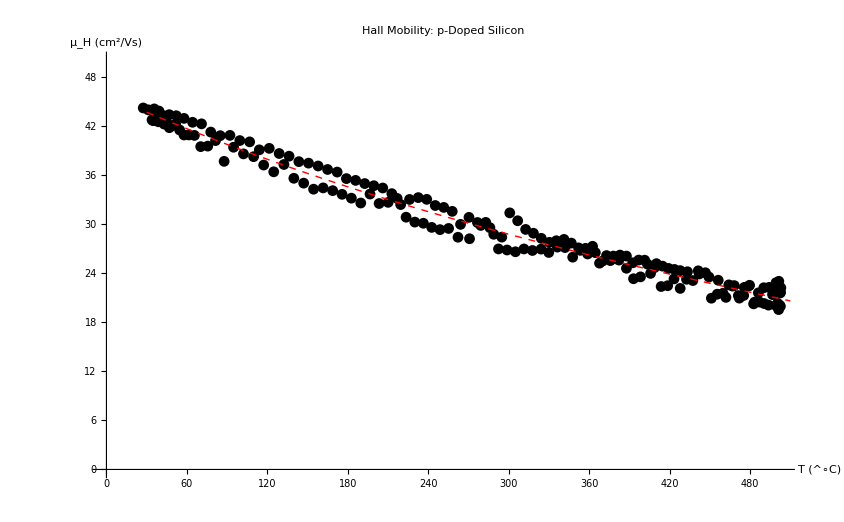

```mathematica
Show[ListPlot[Data,PlotRange->{0,50},PlotStyle->Black,AxesLabel->{"T (^∘C)","μ_H (cm^2/Vs)"},PlotLabel->"Hall Mobility: p-Doped Silicon",LabelStyle->{FontFamily->"Arial",27,GrayLevel[0],Bold},Frame->All],Plot[PFit,{x,30,510},PlotStyle->Directive[Red,Thick, Dashed]]]
```